Figure for ps3, p2.

{ⅇ^(-r^2) r^5,1/12 ⅇ^(-r^2) r^9,1/360 ⅇ^(-r^2) r^13}

{1,1,1}

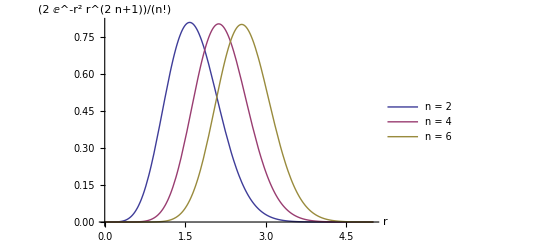

{ps3Fig2.eps,ps3Fig2pn.png}

```mathematica
f[n_,r_] := (2/(n!)) (r^(2n+1)) E^(-r^2) ;

f[#, r] &/@ Range[2,6,2]
Integrate[ f[#, r], {r,0,Infinity} ] &/@ {1,3,5}

p = With[
{nn=Range[2,6,2]},
 Plot[  Evaluate[f[#, r] &/@ nn], {r, 0, 5}, PlotRange -> Full, PlotLegends->Placed[(Row[{"n = ", #}] &/@ nn),{Right, Top}], AxesLabel->{r, f[n,r]}]

]
peeters`exportForLatex["ps3Fig2",p]
```